```mathematica
SurfaceData["Torus","ParametricEquations"][1,2][u,v]
```

{Cos[u] (2+Cos[v]),(2+Cos[v]) Sin[u],Sin[v]}

```mathematica
ColorData["Legacy"]["PrussianBlue"]
```

RGBColor[0.18, 0.18, 0.31]

```mathematica
frames=Table[Rasterize[ParametricPlot3D[{Cos[u] (2+Cos[v]),(2+Cos[v]) Sin[u],Sin[v]},{u,0,2π},{v,0,2π},Mesh->None,PlotStyle-> {RGBColor[0.18, 0.18, 0.31],Specularity[RGBColor[0.18, 0.18, 0.31],10]},Background->RGBColor[0.18, 0.18, 0.31],Axes->False,Boxed->False,Lighting->"Neutral",PlotPoints->100,ViewVector->{0,10Sin[t],10Cos[t]},PlotRange->10,ViewVertical->{1, 0, 0},ViewCenter->{0,0,0}],ImageSize->720,ImageResolution->100],{t,0,2π,1/20}];
```

```mathematica
frames=Table[ParametricPlot3D[{Cos[u] (2+Cos[v]),(2+Cos[v]) Sin[u],Sin[v]},{u,0,2π},{v,0,2π},Mesh->None,PlotStyle-> {RGBColor[0.18, 0.18, 0.31],Specularity[RGBColor[0.18, 0.18, 0.31],10]},Background->RGBColor[0.18, 0.18, 0.31],Axes->False,Boxed->False,Lighting->"Neutral",PlotPoints->100,ViewVector->{0,10Sin[t],10Cos[t]},PlotRange->10,ViewVertical->{1, 0, 0}],{t,0,2π,1/20}];
```

$Aborted

```mathematica
Mesh
```

```mathematica
ListAnimate[frames]
```

```mathematica
computeCurvature[f_]:=Module[{},
fxp=D[ComplexExpand[Re[f]],t];
fyp=D[ComplexExpand[Im[f]],t];
fxpp=D[ComplexExpand[Re[f]],t,t];
fypp=D[ComplexExpand[Im[f]],t,t];
curv=RealAbs[fxp fypp -fyp fxpp]/((fxp^2+fyp^2)^(3/2))];
```

```mathematica
f=Plus@@(#1Exp[I#2 t]&@@RandomVariate[NormalDistribution[],{2,10}]);
```

```mathematica
curv=computeCurvature[f];
max=First@Quiet@FindMaximum[{curv,0≤t≤10},{t,10/2}];
min=First@Quiet@FindMinimum[{curv,0≤t≤10},{t,10/2}];
```

```mathematica
frames=Table[Rasterize[ParametricPlot[ReIm[f],{t,0,tf},Axes->False,PlotRange->5,ColorFunction->Function[{x,y,t},ColorData["CandyColors"][Rescale[curv,{min/2,max/2}]]],ColorFunctionScaling->False,PlotStyle->Thick,AspectRatio->Automatic,Background->Black],ImageSize->720,ImageResolution->100],{tf,.01,10,1/30}];
```

```mathematica
Export["curve.gif",frames,AnimationRepetitions->∞,"DisplayDurations"->1/30]
```

curve.gif

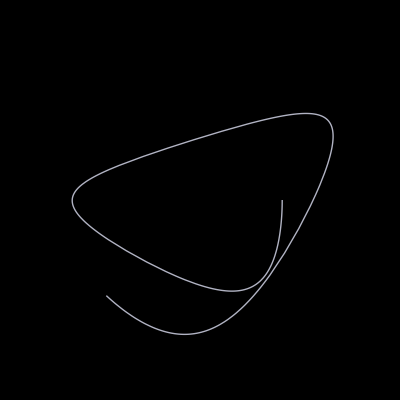

```mathematica
ParametricPlot[ReIm[f],{t,0,10},Axes->False,PlotRange->5,ColorFunction->Function[{x,y,t},ColorData["CandyColors"][Rescale[curv,{min/2,max/2}]]],ColorFunctionScaling->False,PlotStyle->Thick,AspectRatio->Automatic,Background->Black]
```

```mathematica
Export["test.svg",ParametricPlot[ReIm[f],{t,0,10},Axes->False,PlotRange->5,ColorFunction->Function[{x,y,t},ColorData["CandyColors"][Rescale[curv,{min/2,max/2}]]],ColorFunctionScaling->False,PlotStyle->Thick,AspectRatio->Automatic]]
```

test.svg

```mathematica
Export["test.svg",ParametricPlot[ReIm[f],{t,0,10},Axes->False,PlotRange->5,PlotStyle->Thick,AspectRatio->Automatic]]
```

test.svg

```mathematica
Export["curve.gif",frames,AnimationRepetitions->∞,"DisplayDurations"->1/20]
```

curve.gif

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["curve.gif"]]]
```

```mathematica
SystemOpen["curve.gif"]
```

```mathematica
With[{obj=PolyhedronData["Icosahedron"]},Animate[Show[obj,SphericalRegion->True,ViewVector->{5Cos[t],0,5Sin[t]},ViewVertical->{0,1,0}],{t,0,2Pi},AnimationRunning->False]]
```

```mathematica
PolyhedronData["Icosahedron"]
```

-Graphics3D-

```mathematica
Export["ico.obj",%]
```

ico.obj

```mathematica
\[FreakedSmiley]
```

\[FreakedSmiley]

```mathematica
ResourceFunction["BirdSay"]["\[FreakedSmiley]"]
```

\[FreakedSmiley]

```mathematica
Around[.4,]
```

```mathematica
.4±CDF[NormalDistribution[],.975] √((.4( 1-.4))/91)
```

0.4±0.0428929